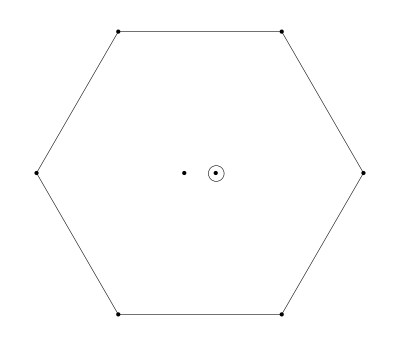

Y=0,  I_3=0

(ud-du)(d̄ū-ūd̄)+2(ds-sd)(d̄s̄-s̄d̄)+(us-su)(s̄ū-ūs̄)

```mathematica
(*-------------------------------*)
```

The current J:

2 (s_a^T C1 d_b) ((d̄)_a 1C((s̄)_b)^T-(d̄)_b 1C((s̄)_a)^T)+2 (d_a^T C1 s_b-s_a^T C1 d_b) ((s̄)_a 1C((d̄)_b)^T)+2 (d_a^T C1 s_b) ((d̄)_b 1C((s̄)_a)^T-(s̄)_b 1C((d̄)_a)^T)-2 (d_a^T C1 s_b(d̄)_a 1C((s̄)_b)^T)+2 (s_a^T C1 d_b(s̄)_b 1C((d̄)_a)^T)+(d_a^T C1 u_b-u_a^T C1 d_b) ((d̄)_a 1C((ū)_b)^T)+(u_a^T C1 d_b-d_a^T C1 u_b) ((ū)_a 1C((d̄)_b)^T)+(u_a^T C1 d_b) ((d̄)_b 1C((ū)_a)^T-(ū)_b 1C((d̄)_a)^T)+(d_a^T C1 u_b) ((ū)_b 1C((d̄)_a)^T-(d̄)_b 1C((ū)_a)^T)+(s_a^T C1 u_b-u_a^T C1 s_b) ((s̄)_a 1C((ū)_b)^T)+(u_a^T C1 s_b-s_a^T C1 u_b) ((ū)_a 1C((s̄)_b)^T)+(u_a^T C1 s_b) ((s̄)_b 1C((ū)_a)^T-(ū)_b 1C((s̄)_a)^T)+(s_a^T C1 u_b) ((ū)_b 1C((s̄)_a)^T-(s̄)_b 1C((ū)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-2 (d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 s)+2 (d̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 d)-2 (d̄ γ^μ d s̄ γ^μ s)+2 (d̄ γ^μ s s̄ γ^μ d)-2 (d̄(γ̄)^5 s s̄(γ̄)^5 d)-d̄ σ^μν d s̄ σ^μν s+d̄ σ^μν s s̄ σ^μν d+(d̄(γ̄)^5 d) (2 (s̄(γ̄)^5 s)-ū(γ̄)^5 u)+(d̄ 1d) (2 (s̄ 1s)-ū 1u)-2 (d̄ 1s s̄ 1d)+d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u-d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d+d̄ γ^μ d ū γ^μ u-d̄ γ^μ u ū γ^μ d+d̄(γ̄)^5 u ū(γ̄)^5 d+1/2 (d̄ σ^μν d ū σ^μν u)-1/2 (d̄ σ^μν u ū σ^μν d)+d̄ 1u ū 1d+s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u-s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s+s̄ γ^μ s ū γ^μ u-s̄ γ^μ u ū γ^μ s-s̄(γ̄)^5 s ū(γ̄)^5 u+s̄(γ̄)^5 u ū(γ̄)^5 s+1/2 (s̄ σ^μν s ū σ^μν u)-1/2 (s̄ σ^μν u ū σ^μν s)-s̄ 1s ū 1u+s̄ 1u ū 1s
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(640 π^6)-(⟨ GG ⟩ log(-q^2/μ^2) q^4)/(16 π^5)-(⟨ ū u⟩ log(-q^2/μ^2) (m_d+m_s+m_u) q^4)/(6 π^4)-(⟨ s̄ s⟩ log(-q^2/μ^2) (8 m_d+5 m_s+2 m_u) q^4)/(12 π^4)-(⟨ d̄ d⟩ log(-q^2/μ^2) (5 m_d+8 m_s+2 m_u) q^4)/(12 π^4)-(5 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(6 π^2)-(5 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/(6 π^2)-(⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(⟨G^3⟩ log(-q^2/μ^2) q^2)/(72 π^6)+(5 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/π^2+(2 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(2 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2-(5 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(6 π^2)-(17 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(6 π^2)-(⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)-(17 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(6 π^2)-(5 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(6 π^2)-(⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)-(⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)-(⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)-(⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)-(5 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(18 π q^2)-(5 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(18 π q^2)-(⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)-(5 ⟨ d̄ Gd⟩^2)/(96 π^2 q^2)-(5 ⟨ s̄ Gs⟩^2)/(96 π^2 q^2)-⟨ ū Gu⟩^2/(48 π^2 q^2)+(7 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(9 π q^2)+(4 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)+(4 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)+(115 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(144 π^2 q^2)+(71 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(288 π^2 q^2)+(71 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(288 π^2 q^2)-(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (-10 m_d-8 m_s))/(9 q^2)+(8 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (8 m_d+10 m_s))/(9 q^2)-(2 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (-10 m_d-8 m_u))/(9 q^2)-(2 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (-10 m_s-8 m_u))/(9 q^2)+(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (2 m_d+2 m_s-m_u))/(3 q^2)+(2 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (8 m_d+10 m_u))/(9 q^2)+(2 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (8 m_s+10 m_u))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

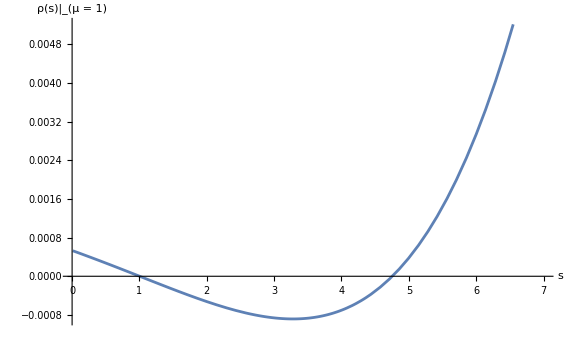
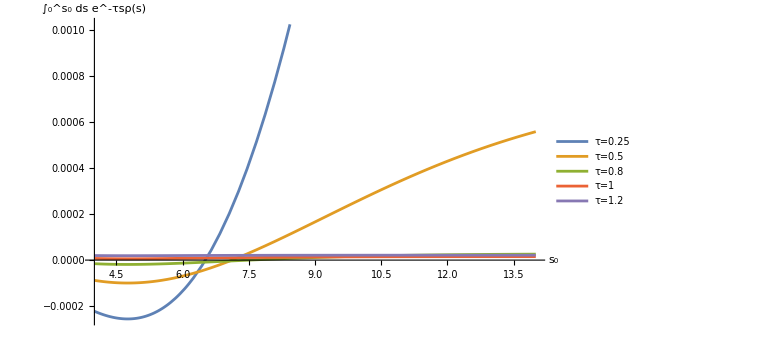

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

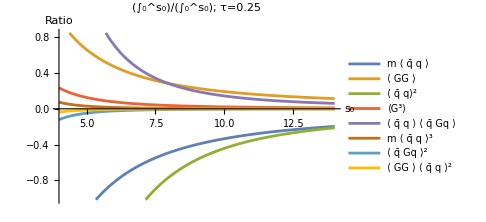
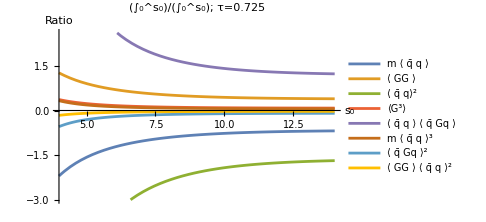
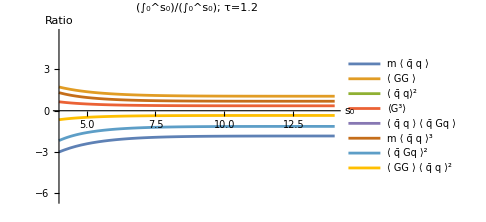

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

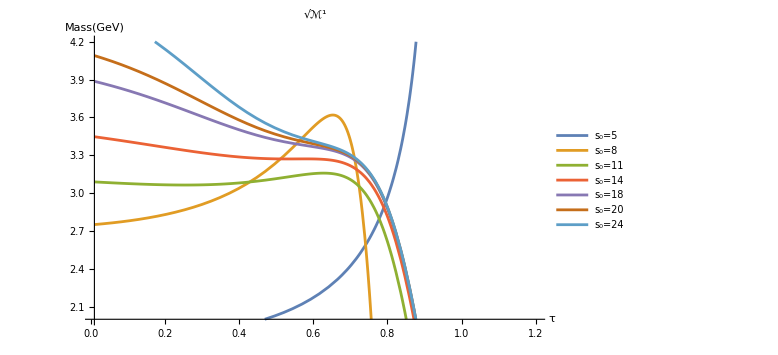
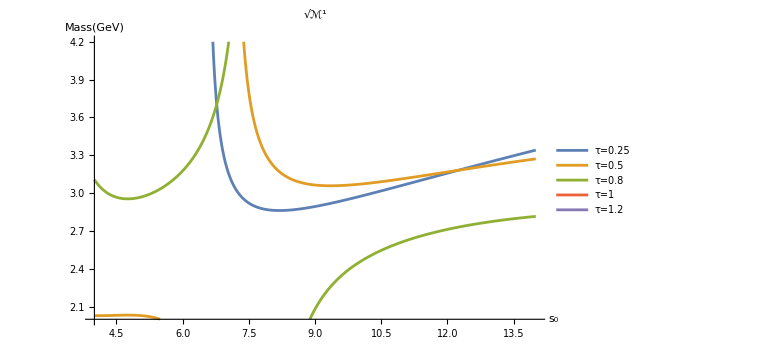

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

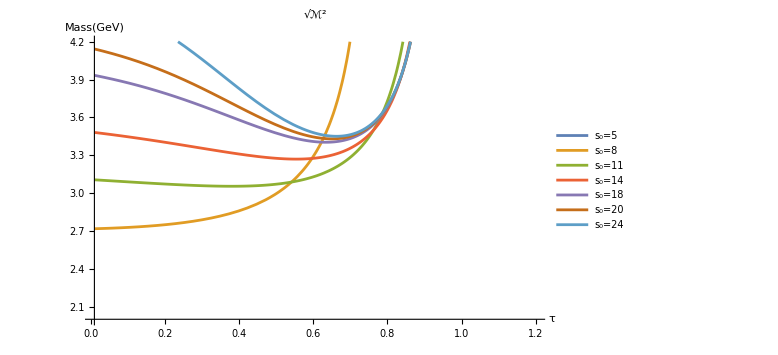
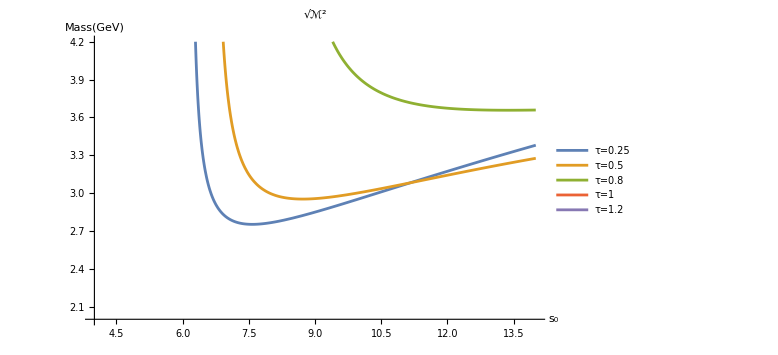

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

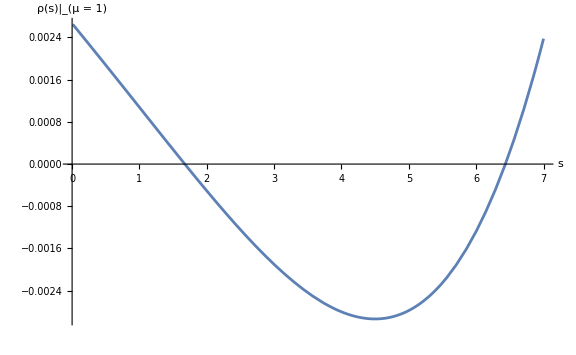
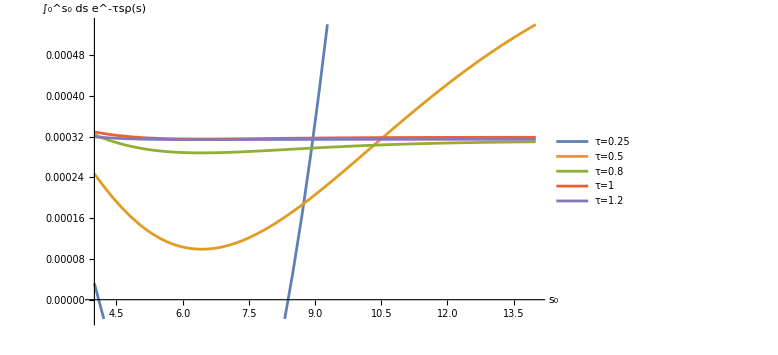

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

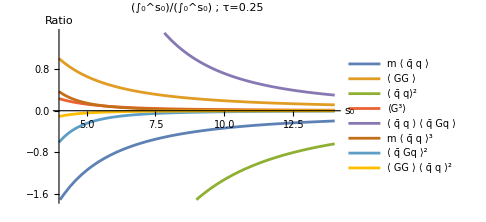
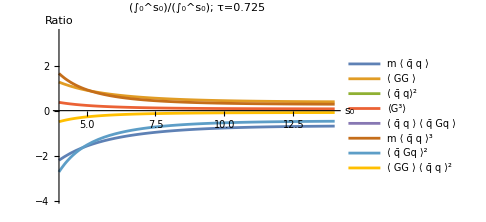
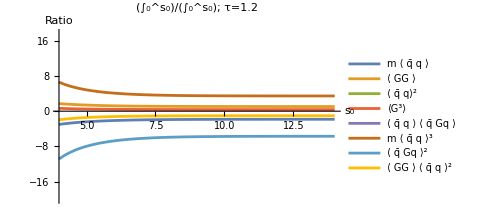

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

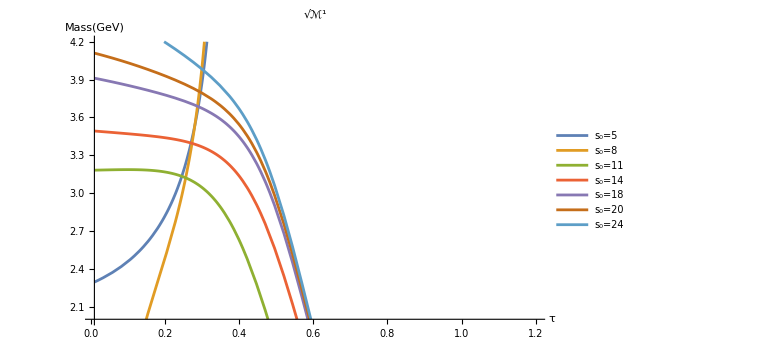
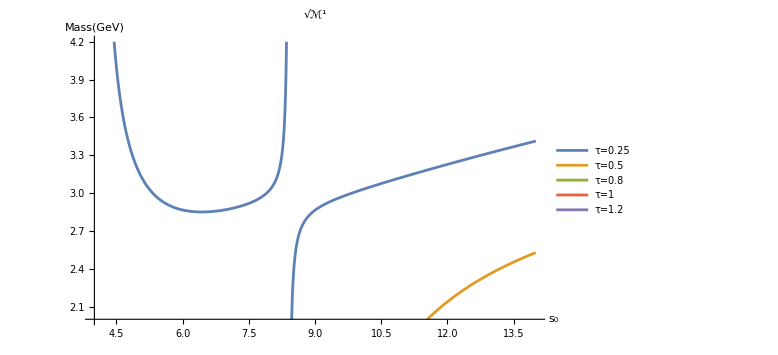

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5